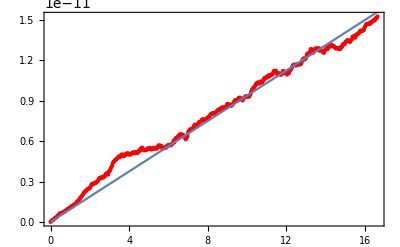

9.3809×10^-13

1.42579×10^-23

```mathematica
data = Import["C:\\Users\\jerem\\workspace\\physics\\BrownianAnalysis\\data\\results\\result.csv"];
ListPlot[data, Joined->True];
lm=LinearModelFit[data,{x},x, IncludeConstantBasis->False];
Show[ListPlot[data,PlotStyle->Red],Plot[lm[x],{x,0,400}],Frame->True]
Normal[lm];
slope = lm["BestFitParameters"];
lm["ParameterTable"];
n = 936*10^(-6);
a = 1.02*10^(-6);
T = 296.01;
s = Part[slope,1]
k = (6*π*n*a*s)/(4*T)
```